# Computação Natural - Aula 02 - Computação Evolutiva

## Algoritmo Genético Padrão

```mathematica
RouletteSelection[pool_,fitness_,n_]:=With[{p=fitness/Total[fitness]},RandomChoice[p-> pool,n]];
```

```mathematica
AG[pop_List,fFun_,cFun_,mFun_,pm_,maxit_Integer,fGoal_:Infinity,sType_:All,showHistory_:False]:=
Module[{population=pop,popfitness=fFun[#]&/@pop,offspring={},offfitness,L=Length[pop],history={},i=1},
history=Join[history,{{MapThread[List,{population,popfitness}],Max[popfitness],Mean[popfitness]}}];
While[i≤maxit&&Max[popfitness]<fGoal,
offspring=mFun[cFun[population],pm];
offfitness=fFun[#]&/@offspring;
If[sType==All,
population=RouletteSelection[Join[population,offspring],Join[popfitness,offfitness],L],
population=RouletteSelection[offspring,offfitness,L]
];
popfitness=fFun[#]&/@population;
history=Join[history,{{MapThread[List,{population,popfitness}],Max[popfitness],Mean[popfitness]}}];
i++;
];
With[{M=Max[popfitness]},
If[!showHistory,
{MapThread[List,{population,popfitness}],M,Mean[popfitness]},
history
]
]
];
```

```mathematica
FitnessReport[historico_]:=Transpose[{#⟦2⟧,#⟦3⟧}&/@historico];
```

```mathematica
BestReport[historico_]:=Table[g⟦1⟧⟦First[Flatten[Position[g⟦2⟧,Max[g⟦2⟧]]]]⟧,{g,Transpose[#⟦1⟧]&/@historico}];
```

## Exemplo 1: Maximizar a função g(x) = 2^(-2((x-0,1)/(0,9))^2)·(sen(5π x))^6(Livro-texto, p. 72)

```mathematica
Ex1Funcao[x_]:=2^(-2*(((x-0.1)/0.9)^2))*Sin[5*Pi*x]^6;
```

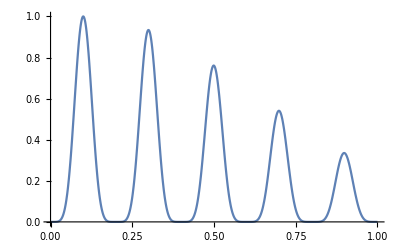

```mathematica
Plot[Ex1Funcao[x],{x,0,1}]
```

### Representação de um indivíduo

Utilizaremos o vetor binário b=(b_1,...,b_10) como genótipo, que representará o fenótipo x = ∑_(i=1)^10 b_i 2^-i.
Quais os valores máximos e mínimos representados? Qual o “passo” entre um valor e o próximo?

### Funções de Fitness, Crossover e Mutação

```mathematica
Ex1Fitness[b_]:=Ex1Funcao[N@Total[Table[b⟦i⟧*2^(-i),{i,1,10}]]];
```

```mathematica
Ex1Crossover[x_,y_]:=With[{cpoint=RandomInteger[9]},{Join[x⟦1;;cpoint⟧,y⟦cpoint+1;;10⟧],Join[y⟦1;;cpoint⟧,x⟦cpoint+1;;10⟧]}];
Ex1Crossover[population_]:=Flatten[Ex1Crossover[#⟦1⟧,#⟦2⟧]&/@Partition[population,2],1]
```

```mathematica
Ex1Mutation[population_,pm_]:=Table[Table[If[RandomReal[]≤pm,1-x⟦i⟧,x⟦i⟧],{i,1,10}],{x,population}];
```

### Execuções e testes

```mathematica
Ex1PopInicial={{0,1,0,1,1,0,1,1,0,1},{0,0,1,0,1,1,1,0,1,1},{1,1,1,0,0,1,0,1,1,0},{0,0,1,0,1,0,1,1,1,0},{0,1,1,0,0,1,0,1,1,0},{1,0,0,0,0,1,0,0,0,1},{0,1,1,0,1,1,1,1,0,1},{1,0,0,1,0,0,0,0,0,0},{1,0,1,1,1,0,1,0,0,1},{1,0,0,1,0,0,0,1,0,1}};
```

```mathematica
Ex1pm=0.01;
Ex1maxit=100;
ListLinePlot[FitnessReport[AG[Ex1PopInicial,Ex1Fitness,Ex1Crossover,Ex1Mutation,Ex1pm,Ex1maxit,1,All,True]],PlotRange->All]
```

## Exemplo 2: Maximizar a função g(x) = 2^(-2((x-0,1)/(0,9))^2)·(sen(5π x))^6(Livro-texto, p. 72) com outra codificação

```mathematica
Ex2Funcao[x_]:=2^(-2*(((x-0.1)/0.9)^2))*Sin[5*Pi*x]^6;
```

```mathematica
Plot[Ex2Funcao[x],{x,0,1}]
```

-Graphics-

### Representação de um indivíduo

Utilizaremos o vetor decimal d=(d_1,...,d_10) como genótipo, que representará o fenótipo x = ∑_(i=1)^10 d_i 10^-i.
Quais os valores máximos e mínimos representados? Qual o “passo” entre um valor e o próximo?

### Funções de Fitness, Crossover e Mutação

```mathematica
Ex2Fitness[d_]:=Ex1Funcao[N@Total[Table[d⟦i⟧*10^(-i),{i,1,10}]]];
```

```mathematica
Ex2Crossover[x_,y_]:=With[{cpoint=RandomInteger[9]},{Join[x⟦1;;cpoint⟧,y⟦cpoint+1;;10⟧],Join[y⟦1;;cpoint⟧,x⟦cpoint+1;;10⟧]}];
Ex2Crossover[population_]:=Flatten[Ex2Crossover[#⟦1⟧,#⟦2⟧]&/@Partition[population,2],1]
```

```mathematica
Ex2Mutation[population_,pm_]:=Table[Table[If[RandomReal[]≤pm,RandomInteger[9],x⟦i⟧],{i,1,10}],{x,population}];
```

### Execuções e testes

```mathematica
Ex2PopInicial={{5,6,5,9,6,6,1,1,9,8},{1,5,1,1,0,0,7,5,7,1},{6,7,5,0,8,0,2,0,9,8},{5,3,4,6,9,0,8,5,4,2},{6,5,7,3,5,4,3,2,6,0},{7,1,5,1,5,5,9,0,8,7},{5,0,6,9,5,7,5,8,7,2},{8,9,8,3,1,7,2,5,9,8},{4,5,6,5,9,9,8,2,4,2},{9,1,0,4,6,2,2,7,6,1}};
```

```mathematica
Ex2pm=0.01;
Ex2maxit=100;
ListLinePlot[FitnessReport[AG[Ex2PopInicial,Ex2Fitness,Ex2Crossover,Ex2Mutation,Ex2pm,Ex2maxit,1,All,True]],PlotRange->All]
```

## Exemplo 3: Gerar, evolutivamente, um padrão bidimensional

```mathematica
ArrayPlot[{{0,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0},{1,0,0,1},{1,0,0,1},{1,1,1,1},{1,0,0,1},{1,0,0,1}}]
```

-Graphics-

```mathematica
Ex3Alvo={0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,1,1,0,0,1,1,0,0,1};
```

### Representação de um indivíduo

Utilizaremos um vetor binário b=(b_1,...,b_36) como genótipo, que representará o fenótipo abaixo, sendo um bit 1 representado por um quadrado preto e um bit 0 representado por um quadrado branco:

```mathematica
Grid[{{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]},{Subscript[b, 5],Subscript[b, 6],Subscript[b, 7],Subscript[b, 8]},{Subscript[b, 9],Subscript[b, 10],Subscript[b, 11],Subscript[b, 12]},{Subscript[b, 13],Subscript[b, 14],Subscript[b, 15],Subscript[b, 16]},{Subscript[b, 17],Subscript[b, 18],Subscript[b, 19],Subscript[b, 20]},{Subscript[b, 21],Subscript[b, 22],Subscript[b, 23],Subscript[b, 24]},{Subscript[b, 25],Subscript[b, 26],Subscript[b, 27],Subscript[b, 28]},{Subscript[b, 29],Subscript[b, 30],Subscript[b, 31],Subscript[b, 32]},{Subscript[b, 33],Subscript[b, 34],Subscript[b, 35],Subscript[b, 36]}},Frame->All]
```

b_1 | b_2 | b_3 | b_4
b_5 | b_6 | b_7 | b_8
b_9 | b_10 | b_11 | b_12
b_13 | b_14 | b_15 | b_16
b_17 | b_18 | b_19 | b_20
b_21 | b_22 | b_23 | b_24
b_25 | b_26 | b_27 | b_28
b_29 | b_30 | b_31 | b_32
b_33 | b_34 | b_35 | b_36

### Funções de Fitness, Crossover e Mutação

```mathematica
Ex3Fitness[d_]:=36-HammingDistance[d,Ex3Alvo];
```

```mathematica
Ex3Crossover[x_,y_]:=With[{cpoint=RandomInteger[35]},{Join[x⟦1;;cpoint⟧,y⟦cpoint+1;;36⟧],Join[y⟦1;;cpoint⟧,x⟦cpoint+1;;36⟧]}];
Ex3Crossover[population_]:=Flatten[Ex3Crossover[#⟦1⟧,#⟦2⟧]&/@Partition[population,2],1]
```

```mathematica
Ex3Mutation[population_,pm_]:=Table[Table[If[RandomReal[]≤pm,1-x⟦i⟧,x⟦i⟧],{i,1,36}],{x,population}];
```

### Execuções e testes

```mathematica
Ex3PopSize=1000;
Ex3PopInicial=Table[RandomInteger[1,36],{Ex3PopSize}];
```

```mathematica
Ex3pm=0.01;
Ex3maxit=100;
Ex3Historico=AG[Ex3PopInicial,Ex3Fitness,Ex3Crossover,Ex3Mutation,Ex3pm,Ex3maxit,36,All,True];
ListLinePlot[FitnessReport[Ex3Historico],PlotRange->{0,36}]
```

### Visualização dos melhores de cada visualização

```mathematica
ListAnimate[ArrayPlot[Partition[#,4]]&/@BestReport[Ex3Historico]]
```

## Exemplo 4: Problema do Caixeiro Viajante

### Mapa das cidades

```mathematica
cidades={{9,9},{3,10},{4,7},{7,7},{1,1},{1,10},{2,9},{2,3},{1,6},{6,9}};
```

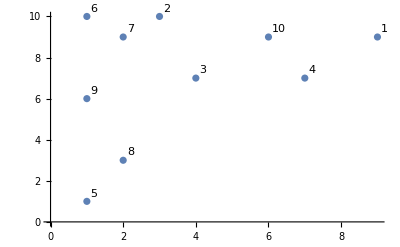

```mathematica
ListPlot[Labeled[#⟦1⟧,#⟦2⟧]&/@MapThread[List,{cidades,Range[1,10]}]]
```

```mathematica
matrizdistancias=Table[N[EuclideanDistance[cidades⟦i⟧,cidades⟦j⟧],4],{i,1,10},{j,1,10}];
MatrixForm[matrizdistancias]
```

(0 | 6.083 | 5.385 | 2.828 | 11.31 | 8.062 | 7. | 9.22 | 8.544 | 3.
6.083 | 0 | 3.162 | 5. | 9.22 | 2. | 1.414 | 7.071 | 4.472 | 3.162
5.385 | 3.162 | 0 | 3. | 6.708 | 4.243 | 2.828 | 4.472 | 3.162 | 2.828
2.828 | 5. | 3. | 0 | 8.485 | 6.708 | 5.385 | 6.403 | 6.083 | 2.236
11.31 | 9.22 | 6.708 | 8.485 | 0 | 9. | 8.062 | 2.236 | 5. | 9.434
8.062 | 2. | 4.243 | 6.708 | 9. | 0 | 1.414 | 7.071 | 4. | 5.099
7. | 1.414 | 2.828 | 5.385 | 8.062 | 1.414 | 0 | 6. | 3.162 | 4.
9.22 | 7.071 | 4.472 | 6.403 | 2.236 | 7.071 | 6. | 0 | 3.162 | 7.211
8.544 | 4.472 | 3.162 | 6.083 | 5. | 4. | 3.162 | 3.162 | 0 | 5.831
3. | 3.162 | 2.828 | 2.236 | 9.434 | 5.099 | 4. | 7.211 | 5.831 | 0)

```mathematica
ComprimentoRota[rota_]:=Total[Table[matrizdistancias⟦rota⟦i⟧,rota⟦i+1⟧⟧,{i,1,9}]]+matrizdistancias⟦rota⟦10⟧,rota⟦1⟧⟧;
```

```mathematica
ComprimentoRota[{1,10,2,6,7,9,5,8,3,4}]
```

30.28

### Representação do indivíduo

Vetor de inteiros (n_1,...,n_10) em que n_i é o número da i-ésima cidade a ser visitada.

### Funções de Fitness, Crossover e Mutação

```mathematica
Ex4Fitness[x_]:=1/ComprimentoRota[x];
```

```mathematica
OrderedReplace[p1_List,p2_List,range_List]:=ReplacePart[p2/.MapThread[Rule,{Complement[Range[1,10],p2⟦#⟧&/@range],Complement[Range[1,10],p1⟦#⟧&/@range]}],MapThread[Rule,{range,p1⟦#⟧&/@range}]];
```

```mathematica
Ex4Crossover[x_,y_]:=With[{range=Range[Min[#],Max[#]]&@{RandomInteger[{1,10}],RandomInteger[{1,10}]}},{OrderedReplace[x,y,range],OrderedReplace[y,x,range]}];
Ex4Crossover[pop_]:=Flatten[Ex4Crossover[#⟦1⟧,#⟦2⟧]&/@Partition[pop,2],1];
```

```mathematica
Ex4Mutation[pop_,pm_]:=Table[If[RandomReal[]≤pm,With[{parts=RandomSample[Range[1,10],2]},ReplacePart[x,{parts⟦1⟧->x⟦parts⟦2⟧⟧,parts⟦2⟧->x⟦parts⟦1⟧⟧}]],x],{x,pop}];
```

### Execuções e testes

```mathematica
Ex4PopSize=100;
Ex4PopInicial=Table[RandomSample[Range[1,10],10],{Ex4PopSize}];
```

```mathematica
Ex4pm=0.2;
Ex4maxit=100;
Ex4Historico=AG[Ex4PopInicial,Ex4Fitness,Ex4Crossover,Ex4Mutation,Ex4pm,Ex4maxit,Infinity,All,True];
ListLinePlot[FitnessReport[Ex4Historico],PlotRange->All]
```

```mathematica
ListLinePlot[1/FitnessReport[Ex4Historico],PlotRange->All]
```

### Visualização dos melhores de cada visualização

```mathematica
Ex4DrawRoute[rota_,fitness_]:=Labeled[Graph[Range[1,10],Join[Table[rota⟦i⟧->rota⟦i+1⟧,{i,1,9}],{rota⟦10⟧->rota⟦1⟧}],VertexCoordinates->cidades,VertexLabels->"Name"],1/fitness]
```

```mathematica
ListAnimate[Ex4DrawRoute[#⟦1⟧,#⟦2⟧]&/@MapThread[List,{BestReport[Ex4Historico],FitnessReport[Ex4Historico]⟦1⟧}]]
```

## Exemplo 5: Problema do Caixeiro Viajante (codificação alternativa)

### Mapa das cidades

```mathematica
cidades={{9,9},{3,10},{4,7},{7,7},{1,1},{1,10},{2,9},{2,3},{1,6},{6,9}};
```

```mathematica
ListPlot[Labeled[#⟦1⟧,#⟦2⟧]&/@MapThread[List,{cidades,Range[1,10]}]]
```

-Graphics-

```mathematica
matrizdistancias=Table[N[EuclideanDistance[cidades⟦i⟧,cidades⟦j⟧],4],{i,1,10},{j,1,10}];
MatrixForm[matrizdistancias]
```

(0 | 6.083 | 5.385 | 2.828 | 11.31 | 8.062 | 7. | 9.22 | 8.544 | 3.
6.083 | 0 | 3.162 | 5. | 9.22 | 2. | 1.414 | 7.071 | 4.472 | 3.162
5.385 | 3.162 | 0 | 3. | 6.708 | 4.243 | 2.828 | 4.472 | 3.162 | 2.828
2.828 | 5. | 3. | 0 | 8.485 | 6.708 | 5.385 | 6.403 | 6.083 | 2.236
11.31 | 9.22 | 6.708 | 8.485 | 0 | 9. | 8.062 | 2.236 | 5. | 9.434
8.062 | 2. | 4.243 | 6.708 | 9. | 0 | 1.414 | 7.071 | 4. | 5.099
7. | 1.414 | 2.828 | 5.385 | 8.062 | 1.414 | 0 | 6. | 3.162 | 4.
9.22 | 7.071 | 4.472 | 6.403 | 2.236 | 7.071 | 6. | 0 | 3.162 | 7.211
8.544 | 4.472 | 3.162 | 6.083 | 5. | 4. | 3.162 | 3.162 | 0 | 5.831
3. | 3.162 | 2.828 | 2.236 | 9.434 | 5.099 | 4. | 7.211 | 5.831 | 0)

```mathematica
ComprimentoPrioridades[prioridades_]:=ComprimentoRota[ReplacePart[Table[0,{10}],Table[Rule[prioridades⟦i⟧,i],{i,1,10}]]];
```

```mathematica
ComprimentoRota[{1,10,2,6,7,9,5,8,3,4}]
```

30.28

```mathematica
ComprimentoPrioridades[{1,3,9,10,7,4,5,8,6,2}]
```

30.28

### Representação do indivíduo

Vetor de inteiros (p_1,...,p_10) em que p_i é a prioridade de visita da i-ésima cidade a ser visitada.

### Funções de Fitness, Crossover e Mutação

```mathematica
Ex5Fitness[x_]:=1/ComprimentoPrioridades[x];
```

```mathematica
Ex5Crossover[x_,y_]:=Ex4Crossover[x,y];
Ex5Crossover[pop_]:=Ex4Crossover[pop];
```

```mathematica
Ex5Mutation[pop_,pm_]:=Ex4Mutation[pop,pm];
```

### Execuções e testes

```mathematica
Ex5PopSize=100;
Ex5PopInicial=Table[RandomSample[Range[1,10],10],{Ex4PopSize}];
```

```mathematica
Ex5pm=0.2;
Ex5maxit=100;
Ex5Historico=AG[Ex5PopInicial,Ex5Fitness,Ex5Crossover,Ex5Mutation,Ex5pm,Ex5maxit,Infinity,All,True];
ListLinePlot[FitnessReport[Ex5Historico],PlotRange->All]
```

```mathematica
ListLinePlot[1/FitnessReport[Ex5Historico],PlotRange->All]
```

### Visualização dos melhores de cada visualização

```mathematica
Ex5DrawRoute[prioridades_,fitness_]:=Module[{rota=ReplacePart[Table[0,{10}],Table[Rule[prioridades⟦i⟧,i],{i,1,10}]]},Labeled[Graph[Range[1,10],Join[Table[rota⟦i⟧->rota⟦i+1⟧,{i,1,9}],{rota⟦10⟧->rota⟦1⟧}],VertexCoordinates->cidades,VertexLabels->"Name"],1/fitness]];
```

```mathematica
ListAnimate[Ex5DrawRoute[#⟦1⟧,#⟦2⟧]&/@MapThread[List,{BestReport[Ex5Historico],FitnessReport[Ex5Historico]⟦1⟧}]]
```